# Лабораторная работа №1 Вариант 2

Выполнила студентка ММФ БГУ 
КМ, 1 к, 5 гр. Бельская Е.А.
  2 сентября 2019

## 2. Ввод и отображение математических выражений

### Задание 2.1

Введите с клавиатуры в ячейку типа Input выражение y (x), представленное ниже.Вариант задания предлагает преподаватель.

```mathematica
y^2(5+2y)^3(1+5y)(9+y^2)^2
```

### Задание 2.2

Ознакомьтесь с различными форматами отображения выражения. Используйте выражение y(x), введенное при выполнении задания 2.1.

```mathematica
y^2*(5 + 2*y)^3*(1 + 5*y)*(9 + y^2)^2
```

Вывод : символы располагаются последовательно друг за другом(1D), вводятся с клавиатуры (Shift-Ctrl-i)

```mathematica
y^2 (2 y+5)^3 (5 y+1) (y^2+9)^2
```

Вывод : выражение отображается в традиционной математической записи(Shift-Ctrl-t)

```mathematica
y^2 (5+2 y)^3 (1+5 y) (9+y^2)^2
```

Вывод :  двумерная структура выражения в стандартах Mathematica, для ввода данных используются палитры ввода данных и сочетания “горячих клавиш”(Shift-Ctrl-n)

```mathematica
y^2(5+2y)^3(1+5y)(9+y^2)^2//FullForm
```

Times[Power[y,2],Power[Plus[5,Times[2,y]],3],Plus[1,Times[5,y]],Power[Plus[9,Power[y,2]],2]]

Вывод : выражение представляется во внутренней форме, в которой с ним работает ядро системы

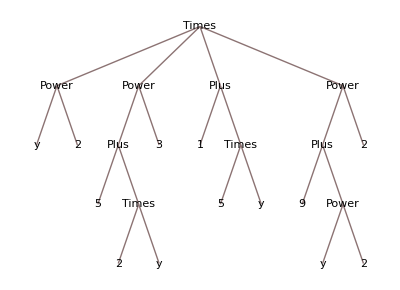

```mathematica
y^2(5+2y)^3(1+5y)(9+y^2)^2//TreeForm
```

## 3. Операции с многочленами

### Задание 3.1

Напишите в текстовых ячейках спецификации1 встроенных функций Expand, Factor, FactorList, CoefficientList, Exponent, выполняющих операции с многочленами. Демонстрационные примеры стройте, используя многочлен из задания 2.1.

```mathematica
myExpr21=y^2(5+2y)^3(1+5y)(9+y^2)^2
?myExpr21
```

y^2 (5+2 y)^3 (1+5 y) (9+y^2)^2

Global`myExpr21

myExpr21=y^2 (5+2 y)^3 (1+5 y) (9+y^2)^2

```mathematica
myExpr21=Expand[myExpr21] (* пример входных параметров*)
```

```mathematica
10125 y^2+62775 y^3+67860 y^4+38898 y^5+17945 y^6+6319 y^7+1530 y^8+308 y^9+40 y^10(*пример выхода*)
```

Данная функция превращает многочлен в сумму одночленов

```mathematica
Length[myExpr21]
```

9

```mathematica
FullForm[myExpr21]
```

Plus[Times[10125,Power[y,2]],Times[62775,Power[y,3]],Times[67860,Power[y,4]],Times[38898,Power[y,5]],Times[17945,Power[y,6]],Times[6319,Power[y,7]],Times[1530,Power[y,8]],Times[308,Power[y,9]],Times[40,Power[y,10]]]

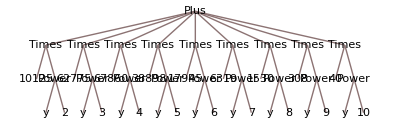

```mathematica
TreeForm[myExpr21]
```

```mathematica
myExpr21=Factor[myExpr21](* пример входных параметров*)
```

```mathematica
y^2 (5+2 y)^3 (1+5 y) (9+y^2)^2(*пример выхода*)
```

Данная функция "сворачивает" в многочлен

```mathematica
FullForm[myExpr21]
```

Times[Power[y,2],Power[Plus[5,Times[2,y]],3],Plus[1,Times[5,y]],Power[Plus[9,Power[y,2]],2]]

```mathematica
TreeForm[myExpr21]
```

-Graphics-

```mathematica
myExpr21//FactorList(* пример входных параметров*)
```

```mathematica
{{1,1},{y,2},{5+2 y,3},{1+5 y,1},{9+y^2,2}}(*пример выхода*)
```

Данная функция дает список факторов многочлена, вместе с их показателями

```mathematica
CoefficientList[myExpr21, y](* пример входных параметров*)
```

```mathematica
{0,0,10125,62775,67860,38898,17945,6319,1530,308,40}  (*пример выхода*)
```

Данная функция даёт список коэффициентов степени (в нашем выражением при переменной y)

```mathematica
Exponent[myExpr21, y](* пример входных параметров*)
```

```mathematica
10(* пример входных параметров*)
```

Данная функция выводит максимальную степень многочлена

### Задание 3.2

Напишите в текстовых ячейках спецификации встроенных функций Apart, Together, ApartSquareFree, выполняющих операции с рациональными функциями. Для демонстрационных примеров используйте многочлен из задания 2.1.

```mathematica
myExpr21=y^2(5+2y)^3(1+5y)(9+y^2)^2
```

```mathematica
Apart[1/myExpr21]
```

1/(10125 y^2)-31/(50625 y)-128/(2139575 (5+2 y)^3)-848768/(15009118625 (5+2 y)^2)-3177645056/(105288967154375 (5+2 y))+1953125/(621441692 (1+5 y))+(3925-1997 y)/(461679354 (9+y^2)^2)+(192615415-65467451 y)/(57282404168196 (9+y^2))

```mathematica
ApartSquareFree[1/myExpr21]
```

1/(10125 y^2)-31/(50625 y)-128/(2139575 (5+2 y)^3)-848768/(15009118625 (5+2 y)^2)-3177645056/(105288967154375 (5+2 y))+1953125/(621441692 (1+5 y))+(3925-1997 y)/(461679354 (9+y^2)^2)+(192615415-65467451 y)/(57282404168196 (9+y^2))

```mathematica
Together[Apart[1/myExpr21]] (*не знаю отличий*)
```

1/(y^2 (5+2 y)^3 (1+5 y) (9+y^2)^2)

### Задание 3.3

Приведите заданное рациональное уравнение к виду :dbc2:dfc9:dbc4:de3a:dbc2:dfeb:dbc4:de3b
:dbc2:dfca:dbc4:de3a:dbc2:dfeb:dbc4:de3b :dbc3:dd4c 0, при этом
числитель P(x) должен быть разложен на множители, до линейных и
квадратичных с отрицательным дискриминантом множителей.
Используйте функции Numerator, Denominator, Factor, Together.

```mathematica
(2x+7)/(x^2+5x-6)+3/(x^2+9x+18)=1/(x+3)
```

```mathematica
Factor[Together[(2x+7)/(x^2+5x-6)+3/(x^2+9x+18)-1/(x+3)]]
```

(8+x)/((-1+x) (6+x))